# Data analysis of the dynamics of states in the GP equation

```mathematica
(*Importing data from julia*)
SetDirectory[NotebookDirectory[]];
datawf=Import["output/wavefunction.dat"];
datawigner=Import["output/wignerfunction.dat"];
datasa=Import["output/survivalamplitude.dat"];
dataneg=Import["output/negativity.dat"];
datafotoc=Import["output/fotoc.dat"];
```

### Classical trajectories

```mathematica
(*Classical Hamiltonian*)
a=-5;
b=1;
mp=10;
H[q_,p_,t_]=p^2/(2*mp) +a*q^2+b*q^4;
```

```mathematica
(*Solving the Hamiltons equation*)
pin=0.01;
qin=0;
tf=5000;
T=0.1;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
(*Classical trajectories and Poncaire sections*)
qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,T}];
```

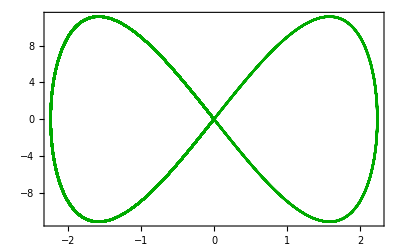

```mathematica
sep=ListPlot[{qp},Joined->True,PlotStyle->Darker[Green],Frame->True]
```

### Wigner function

```mathematica
NN=500;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
L=28;(* Size of the space (must coincide the N in the Julia code)*)
Wvol=Sum[(2*L/NN)*(2*L/NN)*datawigner[[i,3]],{i,1,Length[datawigner]}](*Volume of the Wigner function*)
Wneg=Sum[(2*L/NN)*(2*L/NN)*Abs[datawigner[[i,3]]],{i,1,Length[datawigner]}]-Wvol(*Wigner negativity*)
x2=Sum[(2*L/NN)*(2*L/NN)*datawigner[[i,3]]*datawigner[[i,1]]^2,{i,1,Length[datawigner]}];
p2=Sum[(2*L/NN)*(2*L/NN)*datawigner[[i,3]]*datawigner[[i,2]]^2,{i,1,Length[datawigner]}];
x=Sum[(2*L/NN)*(2*L/NN)*datawigner[[i,3]]*datawigner[[i,1]],{i,1,Length[datawigner]}];
p=Sum[(2*L/NN)*(2*L/NN)*datawigner[[i,3]]*datawigner[[i,2]],{i,1,Length[datawigner]}];
fotoc=(x2-x^2)+(p2-p^2)
```

0.988588

0.0371927

1.90948

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
(*Wigner function and Poncaire sections*)figwigner=Show[ListDensityPlot[datawigner,PlotRange->{{-3,3},{-14,14},All},Frame->  True,LabelStyle->{Black,20},ColorFunction->(FCo[1-0.5/0.35 (#+0.35)]&),ColorFunctionScaling->False,PlotLegends->Automatic],sep]
```

-Graphics-

```mathematica
Export["Fig2r.png",figwigner]
```

Fig2r.png

### Probability Density

```mathematica
(*Probability density*)
datawfn=Table[{datawf[[i,1]],Abs[datawf[[i,2]]+I*datawf[[i,3]]]},{i,1,Length[datawf]}];
```

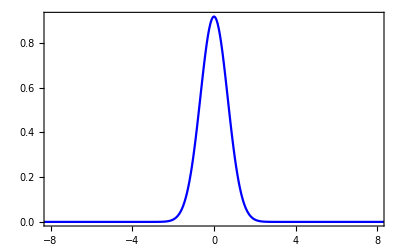

```mathematica
ListPlot[{datawfn},PlotRange->{{-8,8},All},Joined->{True,True},Frame->True,LabelStyle->{Black,15},PlotStyle->{Blue,Red}]
```

### Survival amplitude

```mathematica
ampcomp=Table[datasa[[i,2]]+I*datasa[[i,3]],{i,1,Length[datasa]}];
ratefunction=Table[{datasa[[i,1]],-Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[ampcomp]}];
```

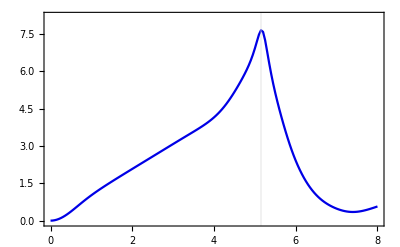

```mathematica
figsa=ListPlot[{ratefunction},PlotRange->{{0,8},{-0.05,8.2}},PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.1],Dashed},{Darker[Blue,0.1],Dotted}},PlotLegends->{},Frame->True,Joined->True,LabelStyle->{18,Black},FrameLabel->{},GridLines->{{5.15},{}},GridLinesStyle->{{Dashed,Gray,Thickness[0.005]},{Thick,Red,Dashed}}]
```

```mathematica
Export["Fig1b.png",figsa]
```

Fig1b.png

```mathematica
5.15/0.05
```

103.

### Fotoc and Wigner negativity

#### Data

```mathematica
(*Data importe from the Julia code*)
datnegm10g0={{0,1*10^-6},{0.1,1.2539702844982514*10^-6},{0.2,1.3447080713380188*10^-6},{0.3,1.5769968334522488*10^-6},{0.4,2.196775773288806*10^-6},{0.5,4.399746093786128*10^-6},{0.6,3.387495848738986*10^-5},{0.7,0.0003178202789687612},{0.8,0.0014666572203445583},{0.9,0.004475090589323383},{1,0.010536605011481015},{1.1,0.02095522658693938},{1.2,0.036991397307119867},{1.3,0.05961541005504545},{1.4,0.09002909696614358},{1.5,0.12903295358258737},{1.6,0.17710361947445885},{1.7,0.2345291594830201},{1.8,0.30188353712848515},{1.9,0.3785799390116974},{2,0.46450530399941026},{2.1,0.5590223238782264}};
datfotocm10g0={{0,3.3618474065164485},{0.1,3.4407966383053576},{0.2,3.678221854269327},{0.3,4.075701915512208},{0.4,4.635359246397046},{0.5,5.359110775025028},{0.6,6.247657826129036},{0.7,7.299274191783263},{0.8,8.508492809849528},{0.9,9.864841087283098},{1,11.351823320963264},{1.1,12.946380427678795},{1.2,14.619053251010302},{1.3,16.33501863485033},{1.4,18.056048602851284},{1.5,19.743269242557503},{1.6,21.360393124437152},{1.7,22.876910719464835},{1.8,24.2706073024225},{1.9,25.52877918096536},{2,26.64770220765964},{2.1,27.630271287978065}};
```

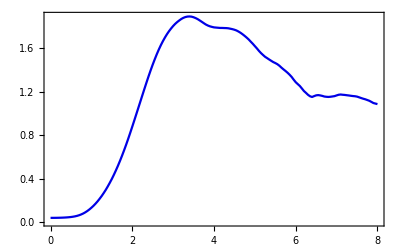

```mathematica
figneg=ListPlot[{dataneg},PlotRange->All,PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.1],Dashed},{Darker[Blue,0.1],Dotted}},PlotLegends->{},Frame->True,Joined->True,LabelStyle->{18,Black},FrameLabel->{},GridLines->{{},{}},GridLinesStyle->{{Dashed,Gray,Thickness[0.005]},{Thick,Red,Dashed}}]
```

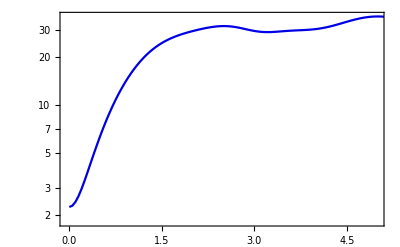

```mathematica
figfotoc=ListLogPlot[{datafotoc},PlotRange->{{-0.05,5},All},PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.1],Dashed},{Darker[Blue,0.1],Dotted}},PlotLegends->{},Frame->True,Joined->True,LabelStyle->{18,Black},FrameLabel->{},GridLines->{{5.15},{}},GridLinesStyle->{{Dashed,Gray,Thickness[0.005]},{Thick,Red,Dashed}}]
```